```mathematica
Clear["Global`*"]
Column@NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../mathematica_plot_options.nb"}]];

lenNode=5;
data=Import[FileNameJoin[{NotebookDirectory[],"result"<>ToString[lenNode]<>".json"}]];
{time,displacement,velocity,modeshape,freq,omega}={"time","displacement","velocity","mode_shape","freq",Sqrt["freq"]}/.data;
```

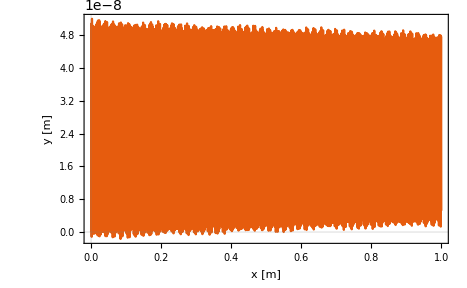

```mathematica
NodeNumber=5;
ListPlot[Table[{time[[i]],displacement[[i,NodeNumber]]},{i,1,Length@time}]
,FrameLabel->{"x [m]","y [m]"}
,Evaluate[plot2Doption]]
```

```mathematica
Animate[
ListPlot[Table[Transpose[{displacement[[t,i+1]],(i-1)/(lenNode-1)}],{i,1,lenNode}]
,PlotMarkers->Automatic
,PlotRange->{0.000001*{-1,1},{-0.1,1}}
,FrameLabel->{"x [m]","y [m]"}
,Evaluate[plot2Doption]
,PlotLabel->Style["StyleBox[\"T\",FontSlant->\"Italic\"]="<>ToString@displacement[[t,1]]]
,Joined->True
,AspectRatio->1.5]
,{t,1,Length[displacement],10}]
```

```mathematica
(*Clear["Global`*"]
Column@NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../mathematica_plot_options.nb"}]];*)getData[lenNode_]:=Module[{time,displacement,velocity,modeshape,freq,omega,data,s,numdata},
data=Import[FileNameJoin[{NotebookDirectory[],"result"<>ToString[lenNode]<>".json"}]];
{time,displacement,velocity,modeshape,freq,omega}={"time","displacement","velocity","mode_shape","freq",Sqrt["freq"]}/.data;
(*superposition[t_]:=Module[{},Sum[modeshape[[i]]*(1-Cos[omega[[i]] t])/omega[[i]]^2,{i,1,Length[freq]}]];*)
s=1;
numdata=1000;
Return@{{Log[#1],Log@#2}&@@@interpolateAndFourier[time[[s;;s+ numdata]],displacement[[s;;s+numdata,Length[displacement[[1]]]-1]]],
Table[Table[{omega[[i]],modeshape[[j]][[i]]},{i,1,Length[omega]}],{j,1,Length[modeshape]}]};
];
data=Table[{i,#1,#2}&@@@getData[i][[1]],{i,{5}}];
ListLinePlot3D[data
,PlotRange->All
,Joined->True]
```

-Graphics3D-

```mathematica
superposition[t_]:=Module[{},Sum[modeshape[[i]]*(1-Cos[omega[[i]] t])/omega[[i]]^2,{i,1,Length[freq]}]];
```

-Graphics3D-

{{0.999948,0.0015374,0.0029027,0.00394487,0.00455159,0.00466109,0.00426711,0.00341715,0.00220541,0.000761745},{-0.0102036,0.147757,0.279886,0.382288,0.44383,0.457567,0.421612,0.339514,0.220011,0.0761538},{0.000104118,-0.281006,-0.444412,-0.421549,-0.221561,0.0718853,0.335208,0.456867,0.384888,0.149473},{-1.06243×10^-6,0.383739,0.421158,0.0782042,-0.335499,-0.445541,-0.151708,0.279869,0.457172,0.218723},{1.08411×10^-8,-0.4448,-0.219949,0.336121,0.385602,-0.14642,-0.457361,-0.0774443,0.419474,0.28202},{-1.10623×10^-10,0.457558,-0.0741967,-0.445376,0.14696,0.421047,-0.216552,-0.384861,0.280863,0.337641},{1.12881×10^-12,-0.420628,0.336992,0.1504,-0.457458,0.216857,0.282997,-0.444319,0.0746842,0.38407},{-1.15185×10^-14,0.33802,-0.457395,0.281082,0.0767119,-0.384769,0.444417,-0.217509,-0.149461,0.420046},{1.17535×10^-16,-0.218705,0.384532,-0.457448,0.41995,-0.281225,0.0748399,0.149438,-0.337651,0.444588},{-1.1871×10^-18,0.0756397,-0.14919,0.218626,-0.282045,0.337722,-0.384157,0.420105,-0.444611,0.457028}}

{2.92053×10^10,1.13638×10^9,1.0447×10^9,9.03046×10^8,7.26829×10^8,5.35193×10^8,3.48914×10^8,1.88145×10^8,7.02522×10^7,7.94882×10^6}

{170896.,33710.2,32321.8,30050.7,26959.8,23134.2,18679.2,13716.6,8381.66,2819.37}

100

1000

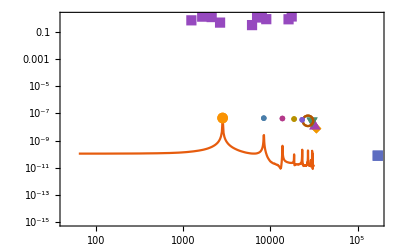

```mathematica
omegaContinuos={10.406861,65.218685,182.614206,357.850959,591.553276,883.678163,1234.228187,1643.203208,2110.603231,2636.428257,3220.678287,3863.353319,4564.453354,5323.978392,6141.928433,7018.303477,7953.103524,8946.328574,9997.978627,11108.053683,12276.553742,13503.478803,14788.828868,16132.603935,17534.804006};
amp=-{0.000000,0.418305,1.142648,1.510970,1.196085,0.302675,-0.724655,-1.354639,-1.259540,-0.493000,0.536586,1.281987,1.347192,0.697430,-0.322471,-1.171166,-1.398172,-0.882997,0.100890,1.031225,1.414169,1.046449,0.123257,-0.865362,-1.394633,-1.183609,-0.344306,0.677760,1.340060,1.291034,0.556705,-0.473131,-1.251823,-1.366024,-0.755119,0.256607,1.132111,1.406677,0.934570,-0.033447,-0.984375,-1.412109,-1.089844,-0.187500,0.812500,1.375000,1.187500,0.375000,-0.750000,-1.500000,-1.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000};

s=100
numdata=1000
ListLogLogPlot[
Join[{{2π*#1,#2}&@@@interpolateAndFourier[time[[s;;s+ numdata]],displacement[[s;;s+numdata,Length[displacement[[1]]]-1]]]},
Table[Table[{omega[[j]],modeshape[[j]][[-1]]*10^-7},{i,1,1}],{j,1,Length[omega]}],
{Table[{omegaContinuos[[i]],amp[[i]]},{i,1,Length[omegaContinuos]}]}]
,Joined->Join[{True},Table[False,{i,50}]]
,PlotMarkers->Join[{None},Table[Automatic,{i,50}]]
,PlotRange->{Automatic,{10^-15,Automatic}}
,Evaluate[plot2Doption]]
```

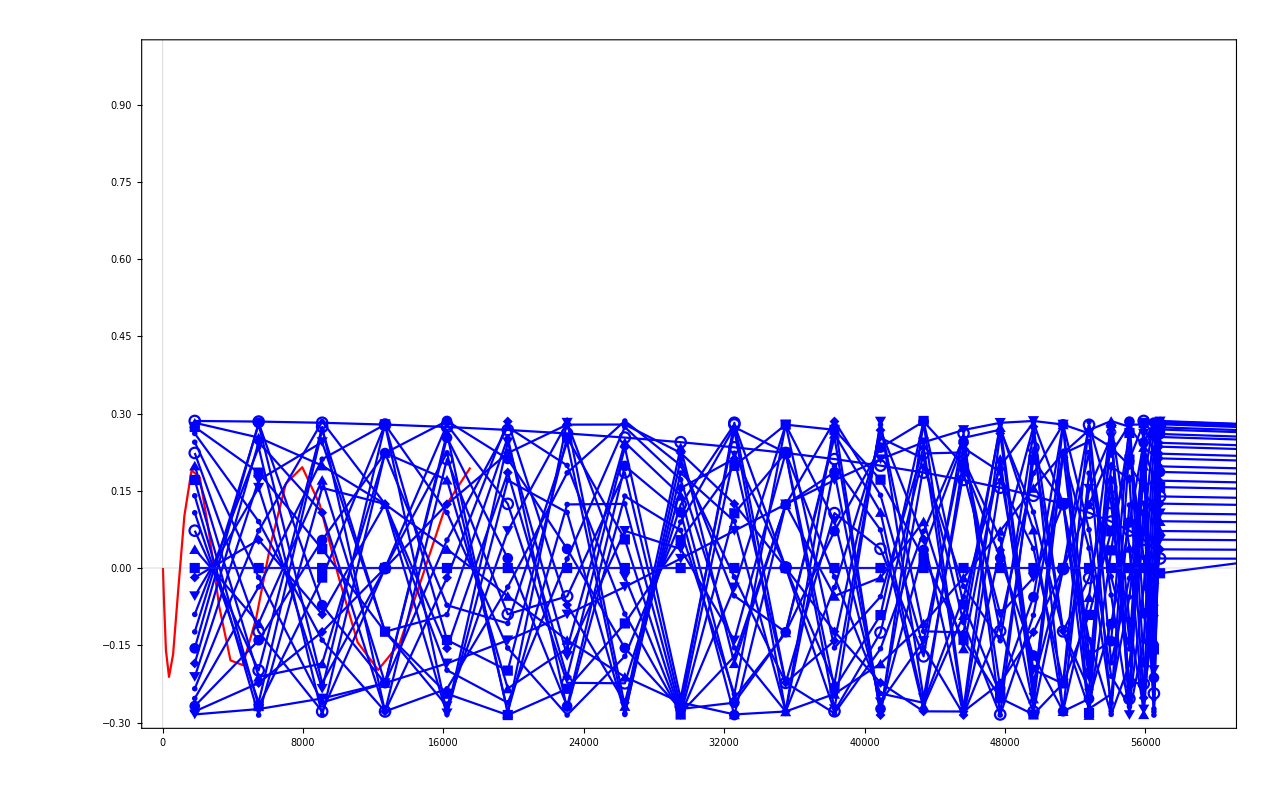

```mathematica
ListPlot[
Join[{Table[{omegaContinuos[[i]],amp[[i]]/Norm[amp]},{i,1,Length[omegaContinuos]}]},
Table[Table[{omega[[i]],modeshape[[j]][[i]]/Norm[modeshape[[j]]]},{i,1,Length[omega]}],{j,1,Length[modeshape]}]
]
,Joined->True
,PlotStyle->Join[{Red},Table[Blue,{i,50}]]
,PlotMarkers->Join[{None},Table[Automatic,{i,50}]]
,PlotRange->{{Automatic,60000},Automatic}
,Evaluate[plot2Doption]]
```

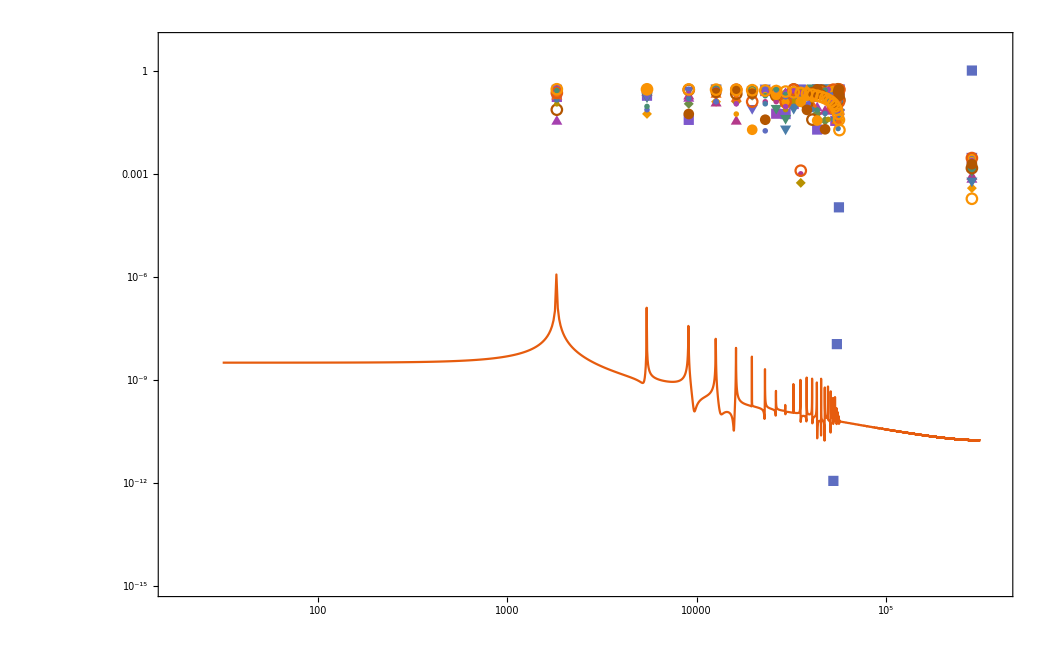

```mathematica
f=474.;
ω=2π*f

f=1406.;
ω=2π*f

f=2302.;
ω=2π*f
```

2978.23

8834.16

14463.9

```mathematica
0.118*2*1000*9.81*0.097
```

224.571

```mathematica
Import[FileNameJoin[{NotebookDirectory[],"result.txt"}]]
Graphics3D[Arrow[{#2,#1}]&@@@list,
PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_ODE/result.txtが見付かりませんでした．

$Failed

-Graphics3D-

-Graphics3D-